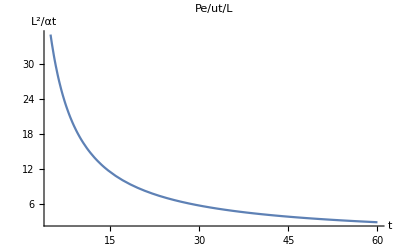

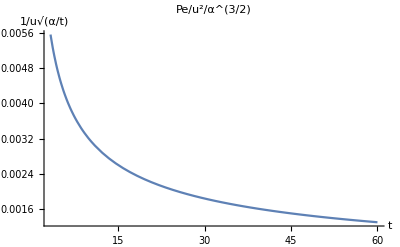

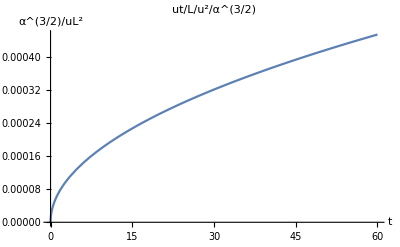

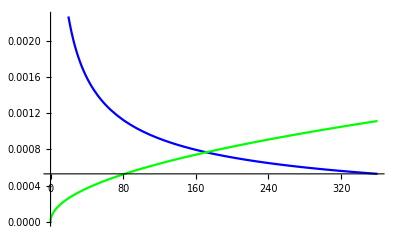

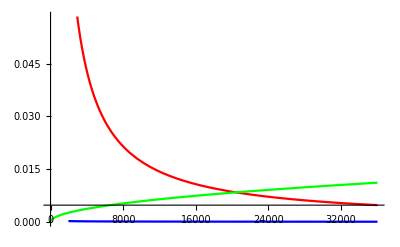

```mathematica
f[t_]=171.459/t;
g[t_]=(1.00724*(10^(-2)))/Sqrt[t];
h[t_]=5.8745*(10^(-5))*Sqrt[t];
Show[{Plot[f[t],{t,0,60}]},PlotRange->All,PlotLabel-> "Pe/ut/L",AxesLabel-> {"t","L^2/αt"}]
Show[{Plot[g[t],{t,0,60}]},PlotRange->All,PlotLabel-> "Pe/u^2/α^(3/2)",AxesLabel-> {"t","1/u√(α/t)"}]
Show[{Plot[h[t],{t,0,60}]},PlotRange->All,PlotLabel-> "ut/L/u^2/α^(3/2)",AxesLabel-> {"t","α^(3/2)/uL^2"}]
plot2=Show[{Plot[f[t],{t,0,36000},PlotStyle->Red]},
{Plot[g[t],{t,0,36000},PlotStyle->Blue]},
{Plot[h[t],{t,0,36000},PlotStyle->Green]},PlotRange->All];
plot1=Show[
{Plot[g[t],{t,0,360},PlotStyle->Blue]},
{Plot[h[t],{t,0,360},PlotStyle->Green]},PlotRange->All];
Needs["PlotLegends`"]
ShowLegend[plot1,{{{Graphics[{Green,Line[{{0,0},{2,0}}]}],"Pe/u^2/α^(3/2)"},{Graphics[{Blue,Line[{{0,0},{2,0}}]}],"ut/L/u^2/α^(3/2)"}},LegendPosition->{0.6,0.2},LegendSize->{0.75,0.75},LegendShadow->False}]
ShowLegend[plot2,{{{Graphics[{Red,Line[{{0,0},{2,0}}]}], "Pe/ut/L"},{Graphics[{Green,Line[{{0,0},{2,0}}]}],"Pe/u^2/α^(3/2)"},{Graphics[{Blue,Line[{{0,0},{2,0}}]}],"ut/L/u^2/α^(3/2)"}},LegendPosition->{0.6,0.2},LegendSize->{0.75,0.75},LegendShadow->False}]
```